# Vaje za 3. teden

6.  3.  2025

## Naloga 0

Napiši  funkcijo quickSort, ki sprejme seznam in vrne urejen seznam. Za urejanje naj uporabi algoritem quick sort

```mathematica
QuickSort[sez_]:=
If[Length[sez] <= 1, sez,
Module[{sezManjse, sezEnako, sezVecje},
sezManjse = Select[sez, # < First[sez] &];
sezEnako = Select[sez, # == First[sez] &];
sezVecje = Select[sez, # > First[sez] &];
Join[QuickSort[sezManjse], sezEnako, QuickSort[sezVecje]]
]
]
```

```mathematica
seznam = RandomInteger[{-100, 100}, 100]
```

{-13,-79,-53,30,53,-62,36,96,-6,45,-98,33,-7,-44,21,47,76,19,-37,-41,47,38,-51,39,44,61,4,92,75,-46,-65,-95,66,-33,23,-42,30,-29,-72,25,81,-30,39,-25,66,-68,-27,21,-82,20,79,7,-61,76,0,92,100,67,93,93,-81,28,48,38,-81,76,-97,-41,-74,-34,-12,-74,89,-18,74,4,-48,81,36,-41,-21,-72,7,78,-5,-52,45,-46,88,-5,72,-83,-47,-71,-96,-55,41,-96,60,81}

```mathematica
QuickSort[seznam]
```

{-98,-97,-96,-96,-95,-83,-82,-81,-81,-79,-74,-74,-72,-72,-71,-68,-65,-62,-61,-55,-53,-52,-51,-48,-47,-46,-46,-44,-42,-41,-41,-41,-37,-34,-33,-30,-29,-27,-25,-21,-18,-13,-12,-7,-6,-5,-5,0,4,4,7,7,19,20,21,21,23,25,28,30,30,33,36,36,38,38,39,39,41,44,45,45,47,47,48,53,60,61,66,66,67,72,74,75,76,76,76,78,79,81,81,81,88,89,92,92,93,93,96,100}

## Naloga 1

Napišite prepisovalno pravilo, ki bo izračunalo produkt dvečlenika z dvočlenikom. S tem pravilom poenostavi izraz (2x - 4)(3 - 4y).

```mathematica
Zmnozi[prvi_, drugi_] :=(prvi *drugi) /. Times->Expand
```

```mathematica
Zmnozi[1x+4, 3-4y]
```

4+x

```mathematica
prep := {b_ * (c_ + d_):> b*c + b*d};
```

```mathematica
(2x-3)(3+4y) //.prep
```

-9+6 x-12 y+8 x y

## Naloga 2

a) Definiraj funkcijo nakljucnaStevila, ki sprejme naravno število n in vrne seznam naključnih celih števil med -100 in 100 dolžine n.
c) S  pomočjo  prepisovalnih  pravil implementiraj urejanje z mehurčki (Bubble sort).

```mathematica
NakljucnaStevila[n_]:=RandomInteger[{-100, 100}, n]
NakljucnaStevila[10]
```

{-5,-88,-52,87,69,-48,-87,-16,85,-26}

```mathematica
prep:={{a___, b_, c_, d___} /; b>c-> {a, c, b, d}};
```

```mathematica
NakljucnaStevila[10] //. prep
```

{-68,-68,-59,-44,-23,-22,1,56,69,89}

## Naloga 3

- Definiraj funkcijo ZadnjaStevka, ki kot argument sprejme naravno število n in vrne zadnjo števko števila n. (ZadnjaStevka(8138719) vrne 9)
- Definiraj funkcijo PrvaStevka, ki kot argument sprejme naravno število n in vrne prvo števko števila n. (PrvaStevka(8138719) vrne 8)
- Definiraj funkcijo Parabola, ki sprejme koeficiente parabole a, b in c in nariše graf parabole ax^2 + bx + c. Graf naj bo narisan tako, da bo teme parabole vedno vidno na sliki.

```mathematica
ZadnjaStevka[st_]:=Last[IntegerDigits[st]]
```

```mathematica
ZadnjaStevka[152349]
```

9

```mathematica
PrvaStevka[st_]:=First[IntegerDigits[st]]
```

```mathematica
PrvaStevka[9889329832892]
```

9

## Naloga 4

Definiraj naslednje sezname:
- {1/(2^20), 1/(2^19), ..., 1/2, 1, 2, 4, 8, ..., 2^24}
- {{}, {1}, {2}, {3}, ..., {99}, {99}, {98}, ..., {2}, {1}, {}}
- seznam dolžine 100, v katerem je vsak naslednji element za eno mesto bolj natančen približek števila π. ({3, 3.1, 3.14, ...})

## Naloga 5

Definiraj funkcijo, ki je za pozitivne x enaka sin(x)/x, za x manjši ali enak 0 pa je enaka cos(x). Pomagaj si s funkcijo `Piecewise`.

```mathematica
f[x_]:=Piecewise[{{Sin[x]/x, x>0}, {Cos[x], x<=0}}]
```

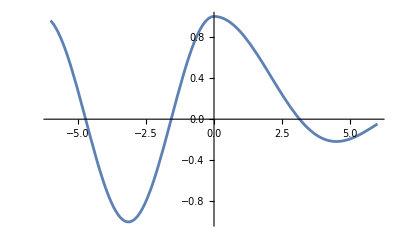

```mathematica
Plot[f[x], {x, -6, 6}]
```

## Naloga 6

Dano je zaporedje  
a) V Mathematici definiraj zaporedje .
b) Definiraj seznam, ki vrne prvih 30 členov zaporedja.
c) Izračunaj limito zaporedja . Izračunaj tudi limito zaporedja . Ali vrsta  konvergira?
d) Izračunaj numerični približek vsote vrste  (uporabi NSum).

```mathematica
a[n_]:=Power[(2n^2 + n + 1) / (2n^2-1), -n^2]
```

```mathematica
prvih30 := Table[a[i],{i, 1, 30} ];
N /@ prvih30
```

{0.25,0.163992,0.0982282,0.0589603,0.0354978,0.0214154,0.0129368,0.00782207,0.00473251,0.00286459,0.00173453,0.00105055,0.000636419,0.000385603,0.000233666,0.000141611,0.0000858304,0.0000520256,0.000031537,0.0000191183,0.0000115904,7.02691×10^-6,4.26037×10^-6,2.58312×10^-6,1.56622×10^-6,9.49668×10^-7,5.75839×10^-7,3.49172×10^-7,2.11731×10^-7,1.28392×10^-7}

```mathematica
Limit[a[n], n-> Infinity]
```

0

```mathematica
Limit[Power[a[n], 1/n], n->Infinity]
```

1/(√ⅇ)

```mathematica
NSum[a[n], {n, 1, Infinity}]
```

0.660849

## Naloga 7

Dano  je  rekurzivno  zaporedje .

a) V Mathematici definiraj zaporedje  z začetnim členom .
b) Izračunaj prvih 5 členova zaporedja . Nato vse vse izraze razširi in združi na skupni ulomek.

## Naloga 8

Za zaporedje  z začetnima členoma  in  izračunajte njegovo limito. Uporabite RSolveValue.

## Naloga 9

Naslednje naloge reši s pomočjo vnosa z naravnim jezikom (brez znanja sintakse Mathematice in brez pomožnih računov). V vseh primerih se prepričaj, da je Mathematica razumela tvoj ukaz. Glej spodnji primer.

### Primer

Izračunaj 20. števko v decimalnem zapisu števila 1+1/2+1/3+...+1/100.

WolframAlphaQueryResults

### Naloge

Določi 443. števko v decimalnem zapisu števila pi.

Izračunaj ploščino območja med krivuljama f(x)=3x^2+2x+1 in g(x)=4-4x^4.

Izračunaj f(3), kjer je f(x)=1+1/x.

Izračunaj obseg elipse s polosema 4 in 3. Ugotovi približno vrednost.

Matej ima 512 jabolk, Jana pa 1024 jabolk. Koliko jabolk imata Matej in Jana skupaj?

Ali je 1009 praštevilo? Izračunaj vsoto 1/2+1/3+1/5+1/7+1/11+...+1/1009. Kaj predstavlja ta vsota?

## Naloga 10

Naslednje naloge reši z vnosom z naravnim jezikom.

### Naloge

Določi površino Slovenije in skupno dolžno njene meje.

Koliko Slovenij prekrije površino Rusije?

Kolikšna je temperatura sonca?